# Eigenthings pt 1 inclass

## Eric Miller - QEA - April 07, 2016

## Definitions

```mathematica
SetDirectory[NotebookDirectory[]];
```

Eventually, these functions may want to use the Notation` package to actually make the subscripted letters have downvalues. For now, I’m just being careful.

```mathematica
Clear@ClearSubscripts
ClearSubscripts[top_]:=(
(Unset[Evaluate[#[[1]]]];Evaluate[#[[1]]])&/@Select[DownValues[Subscript],#[[1,1,1]]==top&]
)
Clear@unknownArray
unknownArray[top_,dim_/;NumberQ[dim]]:=(
Table[Subscript[top, i],{i,dim}]
)
unknownArray[top_,{dim1_/;NumberQ[dim1],dim2_/;NumberQ[dim2]}]:=(
Table[Subscript[top, i,j],{i,dim1},{j,dim2}]
)
```

## Transformation Matrices

```mathematica
A=({{Cos[2θ], Sin[2 θ]}, {Sin[2 θ], -Cos[2 θ]}});
```

```mathematica
FullSimplify@Grid[Eigensystem[A],Frame->All]
```

-1 | 1
{-Tan[θ],1} | {Cot[θ],1}

```mathematica
FullSimplify[Normalize/@FullSimplify/@Eigenvectors[A],{Tan[θ] ∈ Reals,Cot[θ] ∈ Reals,Csc[θ] ∈ Reals}]
```

{{-Tan[θ]/(√(Sec[θ]^2)),1/(√(Sec[θ]^2))},{Cos[θ] Sign[Csc[θ]],1/Abs[Csc[θ]]}}

## Weather

```mathematica
temps=Import["avg_temperatures.mat"][[All,All,1]];
Dimensions@temps
cities={"Boston","Washington DC","SaoPaolo"};
```

{3,7670}

### Plotting

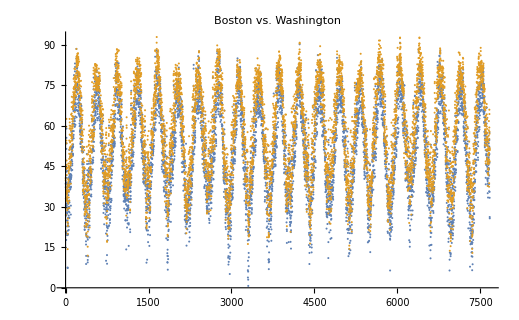

```mathematica
ListPlot[temps[[1;;2]],PlotLabel->"Boston vs. Washington"]
```

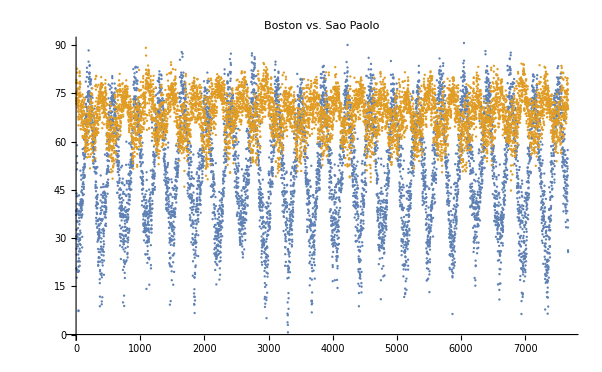

```mathematica
ListPlot[temps[[{1,3}]],PlotLabel->"Boston vs. Sao Paolo"]
```

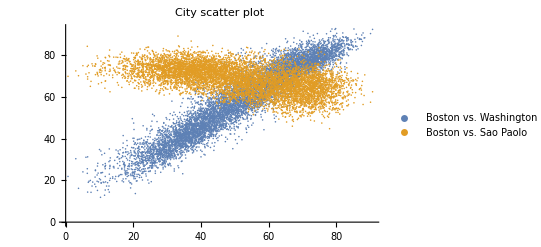

```mathematica
ListPlot[{Transpose@temps[[1;;2]],Transpose@temps[[{1,3}]]},PlotLabel->"City scatter plot",PlotLegends->{"Boston vs. Washington","Boston vs. Sao Paolo"}]
```

### Normalization

```mathematica
normaltemps=(#-Mean[#])&/@temps;
```

### Plotting

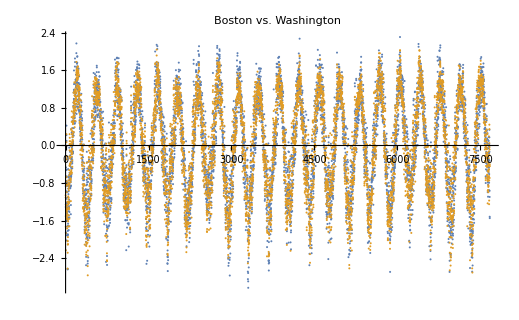

```mathematica
ListPlot[normaltemps[[{1,2}]],PlotLabel->"Boston vs. Washington"]
```

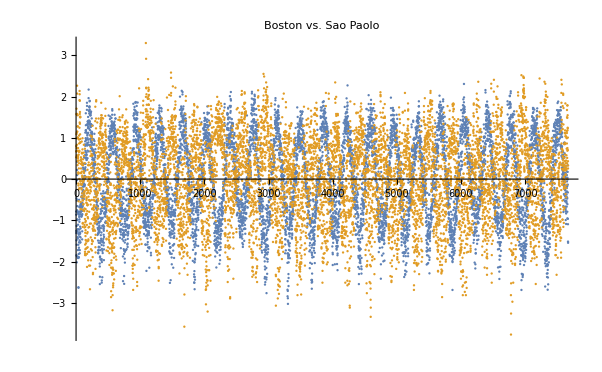

```mathematica
ListPlot[normaltemps[[{1,3}]],PlotLabel->"Boston vs. Sao Paolo"]
```

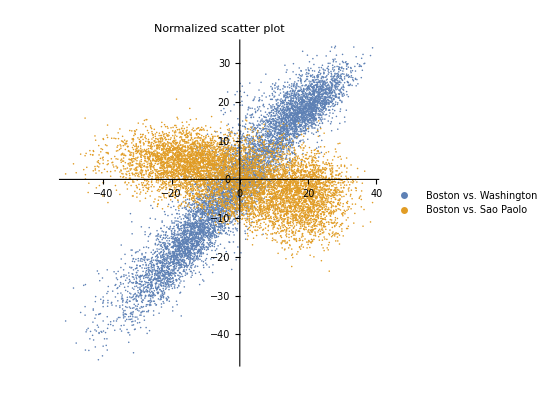

```mathematica
scatterplot=ListPlot[{Transpose@normaltemps[[1;;2]],Transpose@normaltemps[[{1,3}]]},PlotLabel->"Normalized scatter plot",PlotLegends->{"Boston vs. Washington","Boston vs. Sao Paolo"},AspectRatio->1]
```

### Correlation

```mathematica
(cov1=Covariance[Transpose@normaltemps[[{1,2}]]])//MatrixForm
Grid[Transpose@Eigensystem@cov1,Frame->All]
```

(284.891 | 269.393
269.393 | 284.161)

553.919 | {-0.707586,-0.706628}
15.1332 | {0.706628,-0.707586}

```mathematica
cov2=Covariance[Transpose@normaltemps[[{1,3}]]];
cov2//MatrixForm
Grid[Transpose@Eigensystem@cov2,Frame->All]
```

(284.891 | -56.9729
-56.9729 | 39.4645)

297.472 | {-0.976476,0.215624}
26.8838 | {-0.215624,-0.976476}

```mathematica
cov3=Covariance[Transpose@normaltemps[[All]]];
cov3//MatrixForm
Grid[Transpose@Eigensystem@cov3,Frame->All]
```

(284.891 | 269.393 | -56.9729
269.393 | 284.161 | -57.285
-56.9729 | -57.285 | 39.4645)

566.309 | {-0.699356,-0.698516,0.15158}
27.0811 | {0.123325,0.0909659,0.988188}
15.1269 | {0.704054,-0.709789,-0.0225268}

### More plotting

(-0.707586
-0.706628)

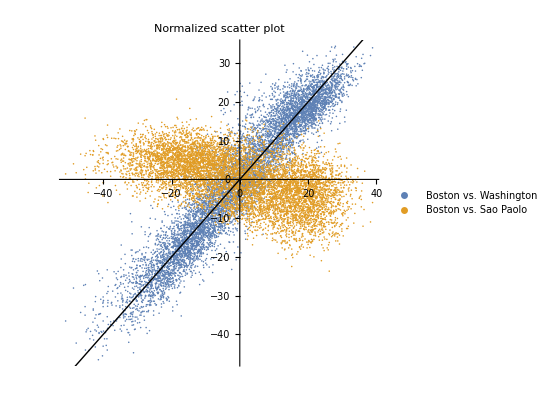

```mathematica
ev1=Eigenvectors[cov1][[1]];
ev1//MatrixForm
Show[scatterplot,Graphics[Line[1000{-ev1,ev1}]]]
```

(-0.976476
0.215624)

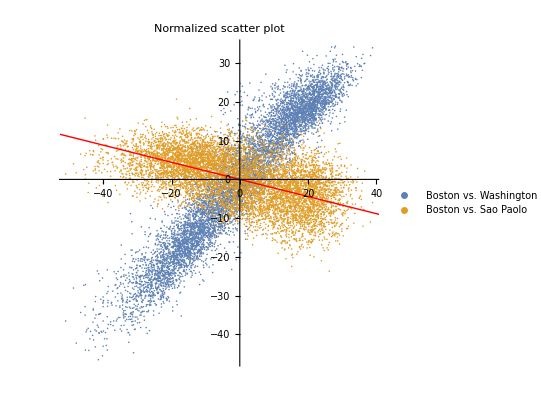

```mathematica
ev2=Eigenvectors[cov2][[1]];
ev2//MatrixForm
Show[scatterplot,Graphics[{Red,Line[100{-ev2,ev2}]}]]
```

### 3D awesomeness!

```mathematica
scatter3=ListPointPlot3D[Transpose@normaltemps,ImageSize->Large,AxesLabel->cities,PlotStyle->{PointSize[.0025]}]
```

-Graphics3D-

```mathematica
{eval,evec}=Eigensystem[Covariance@Transpose@normaltemps];
Grid[{eval,MatrixForm/@evec},Frame->All]
```

566.309 | 27.0811 | 15.1269
(-0.699356
-0.698516
0.15158) | (0.123325
0.0909659
0.988188) | (0.704054
-0.709789
-0.0225268)

```mathematica
lines=MapThread[Graphics3D[{Red, Thick,Line[{{0,0,0},#1 #2}]}]&,{eval,evec}];

Show@@Prepend[lines,scatter3]
```

-Graphics3D-

## Generalized Temperatures

```mathematica
symcities={Entity["City",{"Boston","Massachusetts","UnitedStates"}],Entity["City",{"Washington","DistrictOfColumbia","UnitedStates"}],Entity["City",{"SaoPaulo","SaoPaulo","Brazil"}]}
```

```mathematica
getData[symcities_]:=Module[{data},
data=Map[(QuantityMagnitude@WeatherData[#,"MeanTemperature", {{1995},{2015},"Day"}][[2,1,1]])&,symcities];
data=data[[All,1;;Min[Length/@data]]];
Dimensions@data;
{EntityValue[#,"Name"]&/@symcities,data}
]
```

```mathematica
{names,newtemps}=getData[symcities];
```

```mathematica
barePlot[names_,temps_]:=Module[{normaltemps},
normaltemps=(#-Mean[#])&/@temps;
ListPointPlot3D[Transpose@normaltemps,ImageSize->Large,AxesLabel->names,PlotStyle->{PointSize[.0025]}]
]
fullPlot[names_,temps_]:=Module[{eval,evec,normaltemps,lines},
normaltemps=(#-Mean[#])&/@temps;
{eval,evec}=Eigensystem[Covariance@Transpose@normaltemps];
lines=MapThread[Graphics3D[{Red, Thick,Line[{{0,0,0},#1 #2}]}]&,{eval,evec}];

Show@@Prepend[lines,barePlot[names, temps]]
]
```

```mathematica
fullPlot@@getData@{Entity["City",{"Boston","Massachusetts","UnitedStates"}],Entity["City",{"Tokyo","Tokyo","Japan"}],Entity["City",{"Honolulu","Hawaii","UnitedStates"}]}
```

-Graphics3D-

## Misc

```mathematica
symcities={Entity["City",{"Boston","Massachusetts","UnitedStates"}],Entity["City",{"Washington","DistrictOfColumbia","UnitedStates"}],Entity["City",{"SaoPaulo","SaoPaulo","Brazil"}]}
```

{Boston,Washington,São Paulo}

```mathematica
EntityValue[Entity["City",{"Boston","Massachusetts","UnitedStates"}],"Name"]
```

Boston

```mathematica
data=Map[(QuantityMagnitude@WeatherData[#,"MeanTemperature", {{1995},{2015},"Day"}][[2,1,1]])&,symcities];
data=data[[All,1;;Min[Length/@data]]];
Dimensions@data
```

{3,7645}

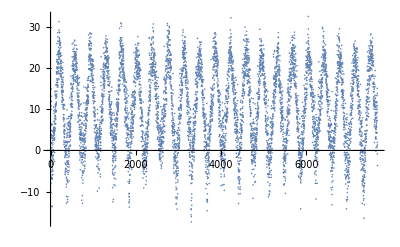

```mathematica
ListPlot@QuantityMagnitude@WeatherData[cities[[1]],"MeanTemperature", {{1995},{2015},"Day"}][[2,1,1]]
```

```mathematica
Hold[While[1+5,Print[λ/.x->5]]]//FullForm
```

Hold[While[Plus[1,5],Print[ReplaceAll[\[Lambda],Rule[x,5]]]]]

```mathematica
FullForm[EvaluationCell[]]
```

CellObject[84913]